```mathematica
Question 1
```

```mathematica
Exact Solution Plots
```

```mathematica
y[x_]:=Sqrt[x]*(BesselJ[(1/6),(8/(3*eps))]*BesselJ[(-1/6),(x^3)/(3*eps)]-BesselJ[(-1/6),8/(3*eps)]*BesselJ[(1/6),(x^3)/(3*eps)])/(BesselJ[(-1/6),1/(3*eps)]*BesselJ[(1/6),8/(3*eps)]-BesselJ[-(1/6),(8/(3*eps))]*BesselJ[1/6,1/(3*eps)]);
```

```mathematica
y[x]
```

(√x (BesselJ[-1/6,x^3/(3 eps)] BesselJ[1/6,8/(3 eps)]-BesselJ[-1/6,8/(3 eps)] BesselJ[1/6,x^3/(3 eps)]))/(-BesselJ[-1/6,8/(3 eps)] BesselJ[1/6,1/(3 eps)]+BesselJ[-1/6,1/(3 eps)] BesselJ[1/6,8/(3 eps)])

```mathematica
E1=Plot[y[x]/.{eps->0.1},{x,1,2},PlotStyle->{Thick,Dashed}];
```

```mathematica
E2=Plot[y[x]/.{eps->0.5},{x,1,2},PlotStyle->{Thick,Dashed}];
```

```mathematica
E3=Plot[y[x]/.{eps->1},{x,1,2},PlotStyle->{Thick,Dashed}];
```

```mathematica
Algrebra for the Approximate Solution
```

```mathematica
TEST[x_]:=(x^-1)*((Exp[(eps^-1)*I*(x^3/3)]-Exp[(eps^(-1))*I*((16-x^3)/3)])/(Exp[(eps^(-1))*I*(1/3)]-Exp[(eps^(-1))*I*5]))
```

```mathematica
Simplify[TEST[x]]
```

(ⅇ^((ⅈ x^3)/(3 eps))-ⅇ^(-(ⅈ (-16+x^3))/(3 eps)))/((ⅇ^(ⅈ/3/eps)-ⅇ^(5 ⅈ/eps)) x)

```mathematica
ExpToTrig[TEST[x]]
```

(Cos[x^3/(3 eps)]-Cos[16/(3 eps)-x^3/(3 eps)]+ⅈ Sin[x^3/(3 eps)]-ⅈ Sin[16/(3 eps)-x^3/(3 eps)])/(x (Cos[1/(3 eps)]-Cos[5/eps]+ⅈ Sin[1/(3 eps)]-ⅈ Sin[5/eps]))

```mathematica
Simplify[Cos[x^3/(3 eps)]-Cos[16/(3 eps)-x^3/(3 eps)]+ⅈ Sin[x^3/(3 eps)]-ⅈ Sin[16/(3 eps)-x^3/(3 eps)]]
```

2 ⅈ (Cos[8/(3 eps)]+ⅈ Sin[8/(3 eps)]) Sin[(-8+x^3)/(3 eps)]

```mathematica
Simplify[(Cos[x^3/(3 eps)]-Cos[16/(3 eps)-x^3/(3 eps)]+ⅈ Sin[x^3/(3 eps)]-ⅈ Sin[16/(3 eps)-x^3/(3 eps)])/(x (Cos[1/(3 eps)]-Cos[5/eps]+ⅈ Sin[1/(3 eps)]-ⅈ Sin[5/eps]))]
```

-(Csc[7/(3 eps)] Sin[(-8+x^3)/(3 eps)])/x

```mathematica
Approximate Solution Plots
```

```mathematica
apr[x_]:=-(Csc[7/(3 eps)] Sin[(-8+x^3)/(3 eps)])/x;
```

```mathematica
A1=Plot[apr[x]/.{eps->0.1},{x,1,2},PlotStyle->Orange];
```

```mathematica
A2=Plot[apr[x]/.{eps->0.5},{x,1,2},PlotStyle->Orange];
```

```mathematica
A3=Plot[apr[x]/.{eps->1},{x,1,2},PlotStyle->Orange];
```

```mathematica
Comparison
```

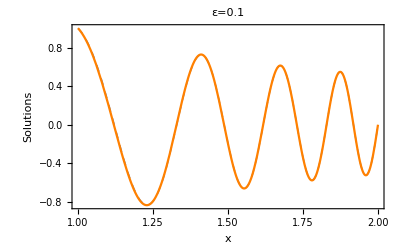

```mathematica
Show[E1,A1,PlotRange->All,Frame->True,FrameLabel->{"x","Solutions"},PlotLabel->"ε=0.1"]
```

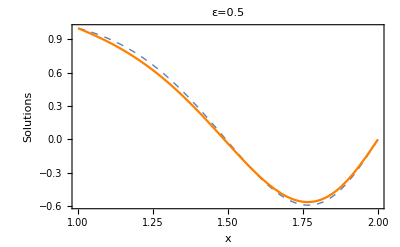

```mathematica
Show[E2,A2,PlotRange->All,Frame->True,FrameLabel->{"x","Solutions"},PlotLabel->"ε=0.5"]
```

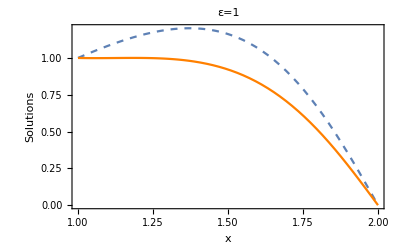

```mathematica
Show[E3,A3,PlotRange->All,Frame->True,FrameLabel->{"x","Solutions"},PlotLabel->"ε=1"]
```

```mathematica
Question 2
```

```mathematica
WRONG
```

```mathematica
delta=0.01;
Y[x_]:=(3*Exp[-(x^2+x)/(2*delta)])*((Exp[1/(delta^2)])/(1-Exp[1/(delta^2)]))*(1/((2*x+1)^1))*(-Exp[(delta^(-1))*((x^2+x)/2)]+Exp[-(delta^(-1))*((x^2+x)/2)]);
```

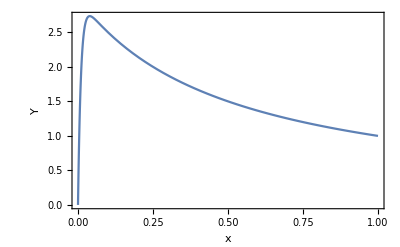

```mathematica
Plot[Y[x],{x,0,1},PlotRange->All,Frame->True,FrameLabel->{"x","Y"}]
```

```mathematica
RIGHT
```

```mathematica
delta=0.01;
```

```mathematica
R[x_]:=Exp[-(x^2+x)/(2*delta)]*((3*Exp[delta^(-2)])/(3-Exp[delta^(-2)]))*(Exp[-(delta^(-1))*((x^2+x)/2)]-((2x+1)^(-1))*Exp[(delta^(-1))*((x^2+x)/2)]);
```

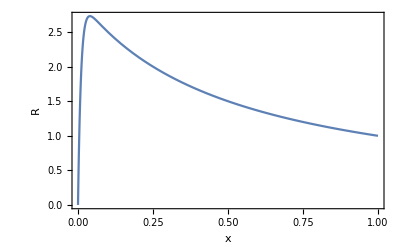

```mathematica
Plot[R[x],{x,0,1},PlotRange->All,Frame->True,FrameLabel->{"x","R"}]
```

```mathematica
ClearAll[B]
```

```mathematica
DSolve[{(eps^2)*B''[x]+(2x+1)*B'[x]+2*B[x]==0,B[0]==0,B[1]==1},B[x],x]
```

{{B[x]→3.68412×10^-10 ⅇ^(-100. x-100. x^2) (-8.29827×10^9+1. Erfi[5. (1.+2. x)])}}

```mathematica
B[x_]:=3.684118811395943*^-10 ⅇ^(-99.99999999999999 x-99.99999999999999 x^2) (-8.298273880676788*^9+1. Erfi[5. (1.+2. x)])
```

```mathematica
eps=0.1
```

0.1

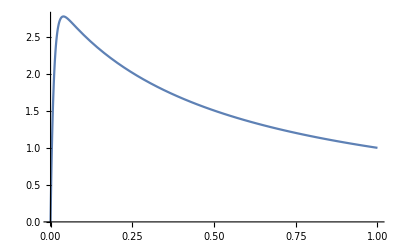

```mathematica
Plot[B[x],{x,0,1}]
```